```mathematica
b=1;
n=1;
```

```mathematica
f[x_,t_,a_]:=(a/b/n*x^n + Exp[-1*((x*Exp[-t*b]-1))^2]-a/b/n*x^n*Exp[-b*t*n])

psi=Table[i,{i,0,15,0.1}];
```

```mathematica
pts =Table[{0,0},{i,100}];
```

```mathematica
For[i=1,i≤100,i++,
pts[[i]]={  psi[[i]],f[ (psi[[i]]),0.1 ,0.05 ]   } ];
```

```mathematica
Dimensions[pts];
```

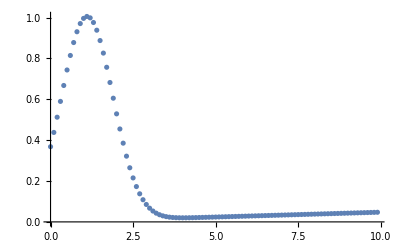

```mathematica
ListPlot[pts]
```

```mathematica
Plot[{f[x,0.1,0],f[x,2,0],f[x,10,0]},{x,0,30},PlotLegends->Placed[{"t=0.1","t=2.0","t=10.0"},{1,.5}],PlotLabel->Style[Framed["solution with a=0"],16,Blue,Background->Lighter[Yellow]]]
```

-Graphics-

```mathematica
Plot[{f[x,0.1,0.05],f[x,2,0.05],f[x,10,0.05]},{x,0,30},PlotLegends->Placed[{"t=0.1","t=2.0","t=10.0"},{1,.5}],PlotLabel->Style[Framed["solution with a=0.05"],16,Blue,Background->Lighter[Yellow]]]
```

-Graphics-